```mathematica
λi[xKAM_][i_]:=BesselJZero[1,i]^2/(16 √xKAM)
ϕi[xKAM_][i_]:=(x↦(√(8λi[xKAM][i]))/(BesselJZero[1,i]BesselJ[2,BesselJZero[1,i]])√x BesselJ[2,4 √(λi[xKAM][i])x^(1/4)])
Clear[δfunctionSolution]
δfunctionSolution[xKAM_,x0_,nmax_:10]:={x,t}↦Sum[
ϕi[xKAM][i][x0]ϕi[xKAM][i][x]Exp[-λi[xKAM][i]t]
,{i,1,nmax}
]
```

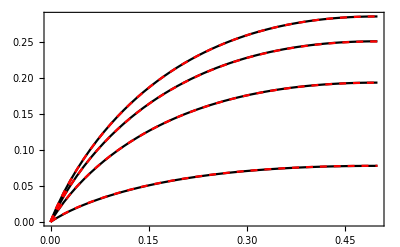

```mathematica
ν1soln=First@NDSolve[{
x^(3/2)Derivative[2,0][ν][x,t]-Derivative[0,1][ν][x,t]==0, 
ν[0,t]==0,
Derivative[1,0][ν][1/2,t]==0,
ν[x,0]==√x  BesselJ[2,4 x^(1/4) √(λi[1/2][1])]
},ν,{x,0,1/2},{t,0,2}];
Plot[
{
Evaluate[Table[ν[x,t],{t,{0,0.1,0.3,1}}]/.ν1soln],
Evaluate[Table[√x  BesselJ[2,4 x^(1/4) √(λi[1/2][1])]Exp[-λi[1/2][1]t],{t,{0,0.1,0.3,1}}]/.ν1soln]
}
,
{x,0,1/2},
Frame->True,PlotStyle->{
Black,Black,Black,Black,
Directive[Dashed,Red],Directive[Dashed,Red],Directive[Dashed,Red],Directive[Dashed,Red]
}]
```

```mathematica
{νδsoln,{fluxPts}}=Reap@NDSolve[
{
x^(3/2)Derivative[2,0][ν][x,t]-Derivative[0,1][ν][x,t]==0, 
ν[0,t]==0,
Derivative[1,0][ν][1/2,t]==0,
ν[x,0]==x^(3/2)/(√(2Pi(1*^-4)^2))Exp[-1/2((x-1/4)/(1*^-4))^2],
WhenEvent[Mod[t,0.01]==0,Sow[{t,Derivative[1,0][ν][0,t]}]]
},ν,{x,0,1/2},{t,0,2}];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
limitExprn=Limit[Evaluate[N[Derivative[1,0][δfunctionSolution[1/2,1/4,5]][x,t]]],x->0,Direction->"FromAbove"];
```

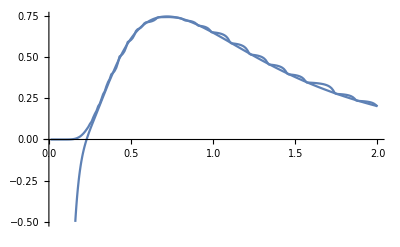

```mathematica
Show[
ListLinePlot[fluxPts],
Plot[limitExprn,{t,0,2}]
,PlotRange->All]
```

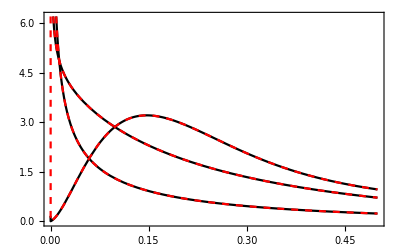

```mathematica
Plot[
{
Evaluate[Table[x^(-3/2)ν[x,t],{t,{0.1,0.3,1}}]/.νδsoln],
Evaluate[N@Table[x^(-3/2)δfunctionSolution[1/2,1/4,9][x,t],{t,{0.1,0.3,1}}]]
}
,
{x,0,1/2},
Frame->True,PlotStyle->{Black,Black,Black,Directive[Dashed,Red],Directive[Dashed,Red],Directive[Dashed,Red]}]
```

```mathematica
(*fSurv[xKAM_,x0_,nmax_:10]:=t↦1-Sum[(1/xKAM)^(1/4)(√2 ϕi[xKAM][i][x0])/BesselJ[2,BesselJZero[1,i]] (1-Exp[-λi[xKAM][i]t]) ,{i,1,nmax}] *)
fSurv[xKAM_,x0_,nmax_:10]:=t↦Sum[√(x0/xKAM)BesselJ[2,4 √(λi[xKAM][i])x0^(1/4)]/BesselJ[2,BesselJZero[1,i]]^2 (Exp[-λi[xKAM][i]t]) ,{i,1,nmax}]
```

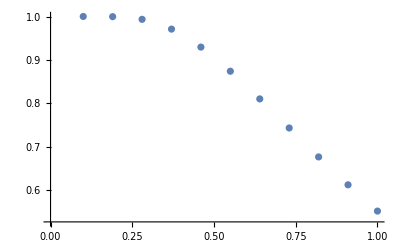

```mathematica
ListPlot[
Table[{t,NIntegrate[Evaluate[N[x^(-3/2)δfunctionSolution[1/2,1/4,9][x,t]]],{x,0,1/2}]},{t,Subdivide[0.1,1,10]}]]
```

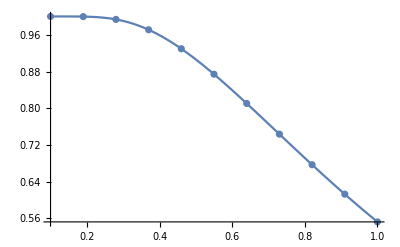

```mathematica
Show[
Plot[Evaluate[N[fSurv[1/2,1/4,10][t]]],{t,0.1,1}],
ListPlot[Table[{t,NIntegrate[Evaluate[N[x^(-3/2)δfunctionSolution[1/2,1/4,10][x,t]]],{x,0,1/2}]},{t,Subdivide[0.1,1,10]}]],
PlotRange->All
]
```